```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages"}]]
```

{/Users/christopher/git/ComputationalDiaries/packages}

```mathematica
Needs["AstronomicalDiaries`"]
```

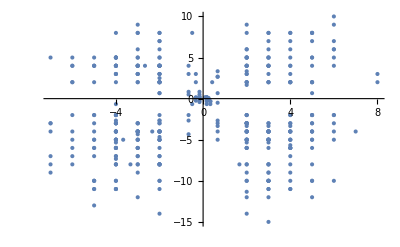

```mathematica
ListPlot[#["Content"]["Displacement"]["EclipticDisplacement"]&/@displacementEvents]
```

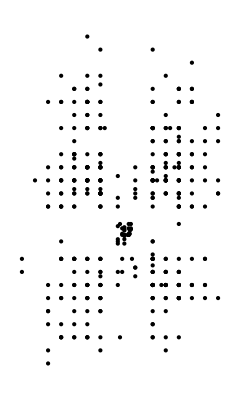

```mathematica
Graphics[Point[DeleteMissing[#["Content"]["Displacement"]["EclipticDisplacement"]&/@displacementEvents,1,2]]]
```

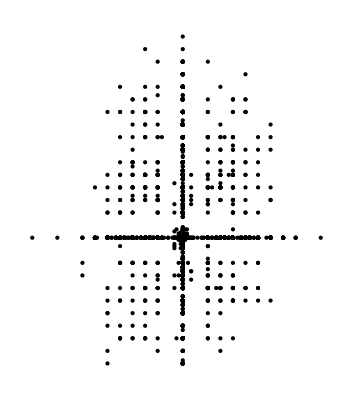

```mathematica
Graphics[Point[(#["Content"]["Displacement"]["EclipticDisplacement"]&/@displacementEvents)/.Missing[]->0]]
```

```mathematica
realObserved={AstronomicalPosition[#["Content"]["Target"],#["Content"]["Date"]]-AstronomicalPosition[#["Content"]["Source"],#["Content"]["Date"]],#["Content"]["Displacement"]["EclipticDisplacement"]}&/@displacementEvents;
```

```mathematica
realObserved={Maybe[Subtract][Maybe[AstronomicalPosition][#["Content"]["Target"],#["Content"]["Date"]],Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]]],#["Content"]["Displacement"]["EclipticDisplacement"]}&/@displacementEvents;
```

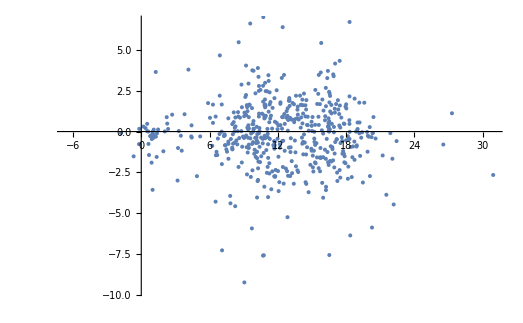

```mathematica
ListPlot[Subtract@@@(DeleteMissing[realObserved,1,2]/.Missing[]->0)]
```

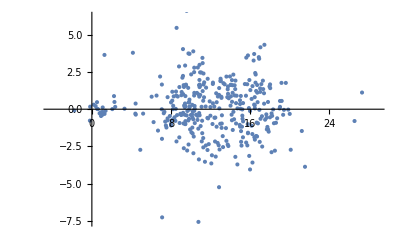

```mathematica
ListPlot[Subtract@@@(DeleteMissing[realObserved,1,3])]
```

```mathematica
#["Content"]["Displacement"]["EclipticDisplacement"]&/@Select[displacementEvents,#["Content"]["Target"]===Entity["Star","Dabih"]&]
```

{{4,2},{5,Missing[]},{-Missing[],Missing[]},{-3,Missing[]},{-Missing[],Missing[]},{Missing[],2},{-3,Missing[]},{-4,Missing[]},{6,Missing[]},{Missing[],Missing[]},{6,Missing[]},{-5,Missing[]},{Missing[],3},{-3,4},{Missing[],Missing[]},{5,4},{3,4},{5,10},{2,Missing[]},{5,7},{Missing[],3},{7,Missing[]},{6,Missing[]},{7,Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},{-5,Missing[]},{-2,Missing[]},{-6,Missing[]},{Missing[],Missing[]},{Missing[],2},{-Missing[],Missing[]},{3,7},{7,7},{-4,Missing[]},{4,Missing[]},{Missing[],8},{-4,Missing[]},{-2,Missing[]},{2,8},{-Missing[],Missing[]},{2,Missing[]},{2,-4},{-Missing[],2},{-3,5},{Missing[],4},{-2,5},{Missing[],4},{2,Missing[]},{2,7},{-7,4},{Missing[],7/3},{Missing[],4},{Missing[],Missing[]},{Missing[],Missing[]},{5,5},{-4,2},{-Missing[],Missing[]},{6,Missing[]},{-Missing[],Missing[]},{2,Missing[]},{Missing[],6},{Missing[],9},{Missing[],5},{Missing[],1/2},{Missing[],Missing[]},{8,Missing[]},{-5,Missing[]},{Missing[],5},{6,6},{-41/6,Missing[]},{-2,6},{Missing[],8},{4,Missing[]},{-4,6},{-Missing[],3},{2,7},{-3,5},{-5,5},{Missing[],5},{16/3,Missing[]},{4,Missing[]},{2,Missing[]},{Missing[],Missing[]},{2,4},{-2,5},{4,5},{-Missing[],5},{3,6},{Missing[],5},{Missing[],4},{-Missing[],9},{-2,Missing[]},{6,Missing[]},{-Missing[],10},{4,8},{Missing[],4},{Missing[],8},{-5,Missing[]},{Missing[],7},{Missing[],5},{-4,17/3},{-Missing[],Missing[]},{4,Missing[]},{-4,Missing[]},{Missing[],Missing[]},{-4,Missing[]},{Missing[],Missing[]},{-5,Missing[]},{Missing[],5},{6,Missing[]},{5,Missing[]},{Missing[],8},{-4,Missing[]},{-6,Missing[]},{-2,Missing[]},{6,Missing[]},{3,Missing[]},{7,Missing[]},{Missing[],16/3},{Missing[],16/3},{Missing[],2},{-8/3,Missing[]},{6,Missing[]},{11,Missing[]},{4,Missing[]},{Missing[],10},{Missing[],17/3},{Missing[],Missing[]},{5,Missing[]},{5,Missing[]},{Missing[],3},{Missing[],5},{Missing[],5},{Missing[],6},{3,Missing[]},{Missing[],4},{Missing[],10/3},{4,Missing[]},{4,Missing[]},{5,Missing[]},{10/3,Missing[]},{-4,Missing[]},{16/3,Missing[]},{Missing[],10},{-4,Missing[]},{-4,Missing[]},{8/3,Missing[]},{-3,Missing[]},{-11/3,Missing[]},{2,Missing[]},{5,Missing[]},{Missing[],5},{Missing[],10},{10/3,Missing[]},{-10/3,Missing[]},{3,Missing[]},{Missing[],Missing[]},{3,Missing[]},{-5,Missing[]},{Missing[],8},{8/3,Missing[]},{-4,Missing[]},{Missing[],4},{Missing[],14/3},{Missing[],2},{2,Missing[]},{5,Missing[]},{-2,Missing[]},{16/3,Missing[]},{-Missing[],14/3},{-6,Missing[]}}

```mathematica
ReverseSort@Counts[#["Content"]["Content"]&/@displacementEvents]
```

<|Missing[KeyAbsent,Content]→3484|>

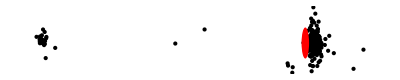

```mathematica
Graphics[{Point[Subtract@@@(DeleteMissing[realObserved,1,2]/.Missing[]->0)],Red,Disk[{0,0},5]}]
```

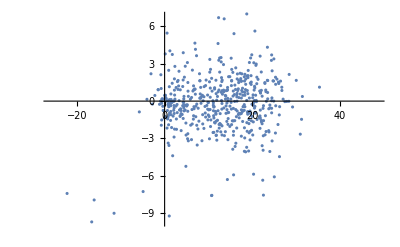

```mathematica
ListPlot[Subtract@@@(DeleteMissing[realObserved,1,2]/.Missing[]->0)]
```

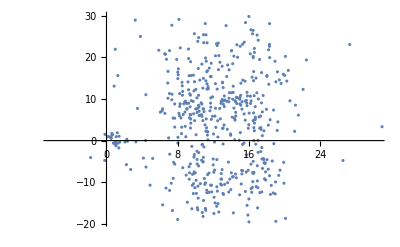

```mathematica
ListPlot[Subtract@@@(DeleteMissing[realObserved,1,2]/.Missing[]->0)]
```

```mathematica
Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]]&@displacementEvents[[7]]
```

Missing[]

```mathematica
Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]]&@displacementEvents[[7]]
```

Missing[]

```mathematica
Maybe[f_][x___]:=f[x]
Maybe[f_][___,m_?MissingQ,___]:=m
```

```mathematica
relations={Transpose[{#["Content"]["Displacement"]["Relations"],#["Degrees"]&/@#["Content"]["Displacement"]["Distances"]}],Maybe[Subtract][Maybe[AstronomicalPosition][#["Content"]["Target"],#["Content"]["Date"]],Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]]]}&/@displacementEvents;
```

```mathematica
relations
```

{{{{Behind,3},{South,9}},{5.07046,8.25995}},{{{Behind,4},{North,6}},{4.55894,-0.532241}},3480,{{{InFrontOf,2},{Missing[],Missing[]}},{14.4267,0.402834}},{{{Above,7/3},{Missing[],Missing[]}},Missing[]}}
 |  |  |  |